# CRNSSA Demo

```mathematica
<<CRNSSA`;
?CRNSSA`*
```

## Reaction System 0: f(x) = 1

```mathematica
rxnsys0 = {
rxn[x,y,1],
rxn[y+y,y,1],
init[{x, y},5]
};
GetSpecies[rxnsys0]
```

{x,y}

{{{5,5},{4,6},{4,5},{4,4},{4,3},{3,4},{3,3},{3,2},{2,3},{1,4},{1,3},{1,2},{1,1},{0,2},{0,1}},{0.,0.0139328,0.0621038,0.092157,0.342408,0.508304,0.572419,0.587488,0.82256,1.26052,1.2805,1.52804,1.61487,6.26392,7.5142}}

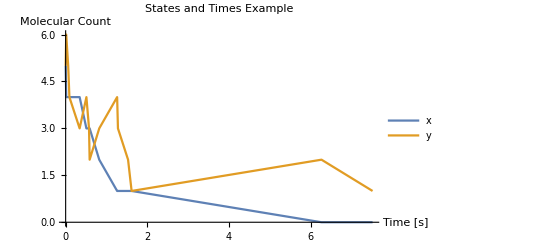

```mathematica
DirectSSA[rxnsys0,outputTS->False]
PlotLastSimulation[PlotLabel->"States and Times Example"]
```

{{5,5},{5,4},{5,3},{5,2},{4,3},{3,4},{3,3},{3,2},{2,3},{1,4},{1,3},{1,2},{0,3},{0,2},{0,1}}

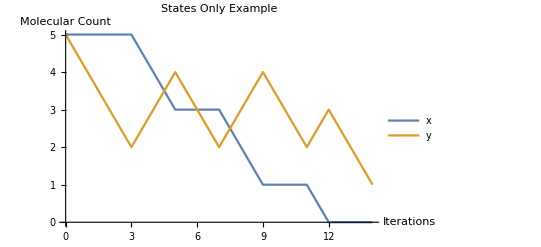

```mathematica
DirectSSA[rxnsys0,statesOnly->True,outputTS->False]
PlotLastSimulation[PlotLabel->"States Only Example"]
```

## Reaction System 1: Demonstrating functionality and automatic processing of objects

```mathematica
rxnsys1={
rxn[0,2x+3y+8z[2,1],3],
revrxn[z[1,2],1,4,5],
init[a, 10],
init[{a,b,x,y},1000]
};
GetSpecies[rxnsys1]
```

{a,b,x,y,z[1,2],z[2,1]}

```mathematica
GetSpecies[rxnsys1, z[_,_]]
```

{z[1,2],z[2,1]}

```mathematica
DirectSSA[rxnsys1,iterEnd->15,useIter->True,statesOnly->True,outputTS->False]
```

{{1010,1000,1000,1000,0,0},{1010,1000,1000,1000,1,0},{1010,1000,1000,1000,2,0},{1010,1000,1000,1000,1,0},{1010,1000,1000,1000,2,0},{1010,1000,1000,1000,1,0},{1010,1000,1000,1000,2,0},{1010,1000,1000,1000,1,0},{1010,1000,1000,1000,2,0},{1010,1000,1000,1000,1,0},{1010,1000,1002,1003,1,8},{1010,1000,1002,1003,0,8},{1010,1000,1002,1003,1,8},{1010,1000,1004,1006,1,16},{1010,1000,1004,1006,0,16},{1010,1000,1004,1006,1,16}}

```mathematica
DirectSSA[rxnsys1,iterEnd->15,useIter->True,finalOnly->True,outputTS->False]
```

{{{1010,1000,1006,1009,0,24}},{1.17785}}

## Reaction System 2: A deterministic CRN

```mathematica
rxnsys2={
rxn[x1,y+z1,2],
rxn[x2,y+z2,2],
rxn[z1+z2,k,1],
rxn[k+y,1,3],
init[x1,5],
init[x2,15]
};
GetSpecies[rxnsys2]
```

{k,x1,x2,y,z1,z2}

TimeSeries[…]

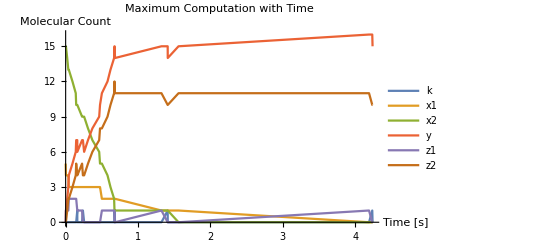

```mathematica
DirectSSA[rxnsys2]
PlotLastSimulation[PlotLabel->"Maximum Computation with Time"]
```

TimeSeries[…]

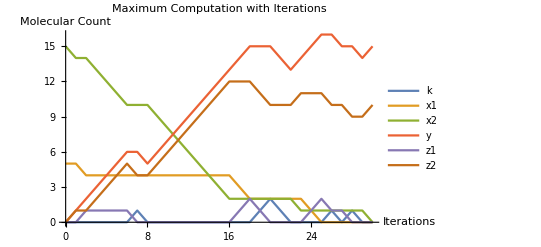

```mathematica
DirectSSA[rxnsys2,statesOnly->True]
PlotLastSimulation[PlotLabel->"Maximum Computation with Iterations"]
```

```mathematica
DirectSSA[rxnsys2,statesOnly->True,finalOnly->True,outputTS->False]
GetSpecies[rxnsys2]
```

{{0,0,0,15,0,10}}

{k,x1,x2,y,z1,z2}

## Reaction System 3: Demonstrating erroneous input handling

```mathematica
rxnsys3={
rxn[a,b,1],
rxn[c,d,2,3],
rxxn[e,f,4],
reaction[g,h,5],
revrxn[i,j,6,7],
revrxn[k,l,8],
init[10],
init[{a,b,c,d, e, f},20],
inits[{g,h, i, j, k, l},30]
};
GetSpecies[rxnsys3]
```

GetSpecies::rxnsyswarn: Warning: Unknown objects detected in rxnsys. These will be ignored by Wolfram pattern matching: {rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],revrxn[k,l,8],init[10],inits[{g,h,i,j,k,l},30]}

{a,b,c,d,e,f,i,j}

```mathematica
DirectSSA[rxnsys3,iterEnd->0.5,useIter->True,finalOnly->True]
PlotLastSimulation[]
```

DirectSSA::rxnsyswarn: Warning: Unknown objects detected in rxnsys. These will be ignored by Wolfram pattern matching: {rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],revrxn[k,l,8],init[10],inits[{g,h,i,j,k,l},30]}

DirectSSA::iterenderr: Error: iterEnd (0.5) must be an integer greater than zero

TimeSeries[…]

PlotLastSimulation::finalonlyerr: Error: Cannot plot when finalOnly = True